```mathematica
(*Project Euler*)
```

```mathematica
(*101: Optimum polynomial*)
F[n_]:=1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10;F/@Range@10
```

{1,683,44287,838861,8138021,51828151,247165843,954437177,3138105961,9090909091}

```mathematica
Fit[Table[{i,i^3},{i,1,10}],{1,x,x^2},x]
```

85.8-76.1 x+16.5 x^2

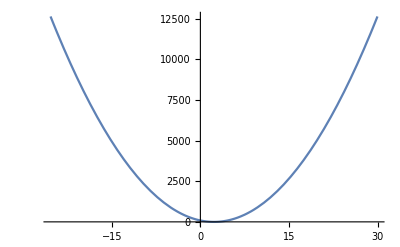

```mathematica
Plot[85.79999999999964-76.0999999999998 x+16.49999999999999 x^2,{x,-25.36666666666661,29.978787878787813}]
```

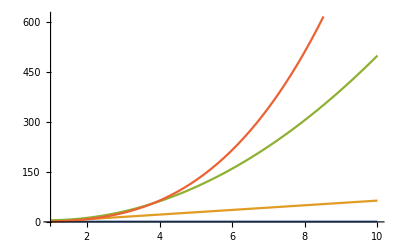

```mathematica
Plot[{1,7*n-6,6*n^2-11*n+10,n^3},{n,1,10}]
```

```mathematica
F[x_,n_]:=Alphabet[][[1;;n+1]].NestList[#*x&,1,n];
```

```mathematica
Solve[,Alphabet[][[1;;10+1]]]
```

Solve::ivar: a is not a valid variable.

Solve[{a+b+c+d+e+f+g+h+i+j+k==1,a+2 b+4 c+8 d+16 e+32 f+64 g+128 h+256 i+512 j+1024 k==8,a+3 b+9 c+27 d+81 e+243 f+729 g+2187 h+6561 i+19683 j+59049 k==27,a+4 b+16 c+64 d+256 e+1024 f+4096 g+16384 h+65536 i+262144 j+1048576 k==64,a+5 b+25 c+125 d+625 e+3125 f+15625 g+78125 h+390625 i+1953125 j+9765625 k==125},{a,b,c,d,e,f,g,h,i,j,k}]

```mathematica
a=1
```

1

```mathematica
ToExpression@F[#[[1]],10]==#[[2]]&/@Table[{i,i^3},{i,1,5}]
```

ToExpression::notstrbox: a+b+c+d+e+f+g+h+i+j+«1» is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: a+2 b+4 c+8 d+16 e+32 f+64 g+128 h+256 i+512 j+«1» is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: a+3 b+9 c+27 d+81 e+243 f+729 g+2187 h+6561 i+19683 j+«1» is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

{$Failed==1,$Failed==8,$Failed==27,$Failed==64,$Failed==125}

```mathematica
ToExpression
```